```mathematica
Guy F. Mongelli, F.E.                                                             ECHE 462
Prof. Sankaran                                                                              3/24/2013
```

```mathematica
Group Assignment #3
```

```mathematica
Problem #3
```

```mathematica
From the solution to the problems 1 and 2, which were performed in Excel by my group members:
```

```mathematica
(* kimp=-6*(200)(2.65/MWSi)/(.2*1.0625/MWHF)^α
```

```mathematica
kimp=9.83926*10^-4;
```

```mathematica
α=1.6737;
```

```mathematica
In problem 3, the initial concentration is given as:
```

```mathematica
per0=20;
```

```mathematica
The area of a single etch is 1000 cm (=10meter)in length multiplied by 0.001 cm ( = 10 microns ) wide.  There is an additional factor of 2 for both sides of the wafer and a factor of 1000 for the number of wafers.
```

```mathematica
A=1000*0.001*2000;
```

```mathematica
A (*cm^2)
```

2000

```mathematica
The volume is simply the area associated with the above process multiplied by the 50 micron depth.
```

```mathematica
V=A*0.005(*50 microns in cm*)
```

10.

```mathematica
A
```

2000.

```mathematica
V (*cm^3*)
```

10.

```mathematica
A/V
```

200.

```mathematica
The molecular weight of the SiO2 and HF are given:
```

```mathematica
MWSi=60.08(*g/m0l*);
```

```mathematica
MWHF=20.01(*g/mol*);
```

```mathematica
The density is corrected as an average of the densities of pute water (assumed 1g/mL ) and pure HF (assumed 1.15 g/mL).
```

```mathematica
rho[x_]=x*0.3125+1;
```

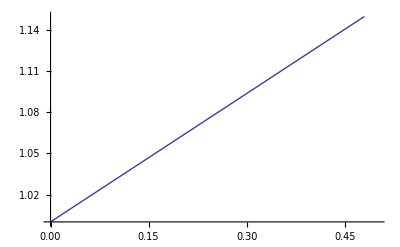

```mathematica
Plot[rho[x],{x,0,0.50},PlotRange->{1,1.15}]
```

```mathematica
It is much easier to solve this problem as a concentration problem. In other words, the initial concentration of HF is known and the concentration when the etch is completed is known from the stoichiometry of the reaction.  Therefore the kinetics can be simplified without inter-relating the density and etch depth as a function of initial and present weight percent then back correlating those functions into time.
```

```mathematica
DSolve[{1/V(A*2.65)/MWSi δ'[per]==-kimp*(per[t]*1.065/100/MWHF)^α,δ[0]==2*10^-5},δ[per],per]
```

DSolve::ivhead: The independent variable per appears in the head of the expression per[t]. The independent variables should always be arguments.

DSolve[{8.82157 δ'[per]==0.0588902 per[t]^1.6737,δ[0]==1/50000},δ[per],per]

```mathematica
DSolve[{1/V(A*2.65)/MWSi δ'[t]==-kimp*(c[t])^α,δ[0]==2*10^-5},δ[t],t]
```

{{δ[t]→(1-50000 ∫_1^0 2013.81 c[K[1]]^1.6737ⅆK[1]+50000 ∫_1^t 2013.81 c[K[1]]^1.6737ⅆK[1])/50000}}

```mathematica
DSolve[{1/V(A*2.65)/MWSi c'[t]==-kimp*(c[t])^α,c[0]==(0.2*1.065)/MWHF},c[t],t]
```

{{c[t]→-29.9767/((7.00997×10^10-4.45739×10^12 t)^(3263/6737) (-0.0157266+1. t))}}

```mathematica
Clear[c[t]]
```

Clear::ssym: c[t] is not a symbol or a string.

```mathematica
Initial concentration(*in g/cm^3):
```

```mathematica
CF0=.20*1.0625/MWHF
```

0.0106197

```mathematica
Initial Number of Moles HF;

HF0=0.2*1.0625/MWHF*500
```

5.30985

```mathematica
Number of Moles HF Reacted;
HFR=V*2.65/MWSi*6
```

2.64647

```mathematica
Final concentration(*in g/mL = g/cm^3):
```

```mathematica
HF1=(HF0-HFR)/500
```

0.00532675

```mathematica
DSolve[{c'[t]==-kimp*(c[t])^α,c[0]==0.0106197},c[t],t]
```

{{c[t]→(2.98478×10^7)/((32238.8+1. t) (1.58603×10^10+491963. t)^(3263/6737))}}

```mathematica
{{c[t]->-0.008571543700447415/((1.2245910576809622*^7-4.1119041388*^10 t)^(3263/6737) (-0.000297816052209413+1. t))}}
```

{{c[t]→-0.00857154/((1.22459×10^7-4.1119×10^10 t)^(3263/6737) (-0.000297816+1. t))}}

```mathematica
c3[t_]=(2.984781401115852*^7)/((32238.82420367651+1. t) (1.5860308671713308*^10+491963. t)^(3263/6737));
```

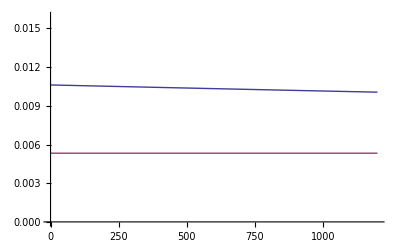

```mathematica
Plot[{c3[t],HF1},{t,0,1200},PlotRange->{0,1.5*CF0}]
```

```mathematica
c3[70]
```

0.00449909